```mathematica
Import["https://quest.qtechtheory.org/QuEST.m"]
```

Circuit drawing can be performed right away, since generated locally in Mathematica.

```mathematica
m = ({{0, ⅈ}, {Exp[.3ⅈ], 0}});

u[θ_]:= Circuit[
 Subscript[S, 5] Subscript[T, 7] Subscript[Y, 8]
Subscript[Ry, 3][θ] Subscript[C, 3][Subscript[Rz, 2][θ]]Subscript[C, 8,7,6][Subscript[Z, 5]] Subscript[M, 0] Subscript[Ry, 3][θ] Subscript[M, 1,3,4] Subscript[SWAP, 0,3] Subscript[C, 5][Subscript[SWAP, 4,6]] Subscript[M, 0] Subscript[H, 2] Subscript[X, 3] Subscript[T, 3] Subscript[C, 0,2,3,4][Subscript[X, 1]] Subscript[C, 0][Subscript[U, 1,7]]Subscript[U, 0][m] Subscript[U, 2,4] Subscript[SWAP, 0,1] Subscript[C, 2,3][Subscript[SWAP, 4,5]] Subscript[U, 3,1] Subscript[U, 4,5] Subscript[U, 6,8] Subscript[X, 0]  Subscript[U, 0,1] Subscript[C, 2,3,4,5][Subscript[T, 6]] Subscript[C, 0,4,5][Subscript[U, 1,2]] Subscript[C, 2,4,5][Subscript[U, 1,3]] Subscript[X, 0] Subscript[C, 6,8][Subscript[U, 7][m]] Subscript[Depol, 2,4][θ/100]  Subscript[Deph, 0][θ/200] Subscript[Depol, 5][θ/300] Subscript[Deph, 6,7][θ/400]];
```

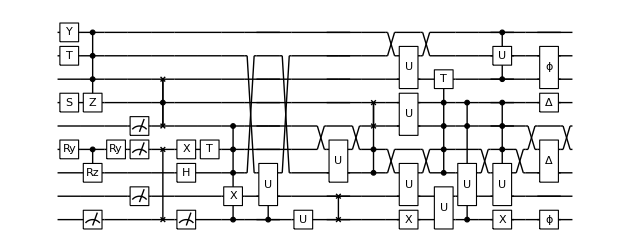

```mathematica
DrawCircuit @ u[θ]
```

Here we remove the gates which aren’t supported by the simulator (2-qubit unitaries)

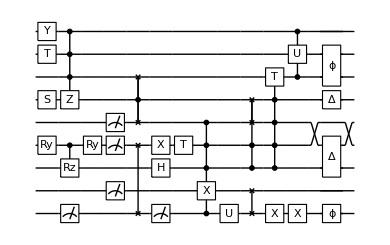

```mathematica
v[θ_] := DeleteCases[u[θ],Subscript[U, _Integer,_Integer]|Subscript[C, __Integer][Subscript[U, _Integer,_Integer]]]
DrawCircuit @ v[θ]
```

We  connect to a QuEST environment, which can be local or remote (for local, we require quest_link is in this directory)

```mathematica
env = CreateLocalQuESTEnv[];
```

```mathematica
?QuEST`*
```

We  can now simulate our sanitised circuit

```mathematica
ρ = CreateDensityQureg[9];
ψ = CreateQureg[9];
```

```mathematica
ApplyCircuit[v[0],InitPlusState @ ψ];
```

```mathematica
params = Range[0,π,.01];
fids = Table[
	ApplyCircuit[v[θ],InitPlusState @ ρ];
	CalcFidelity[ρ, ψ],
	{θ, params}
];
```

Note the results here are random since our circuit contains projective measurement gates.

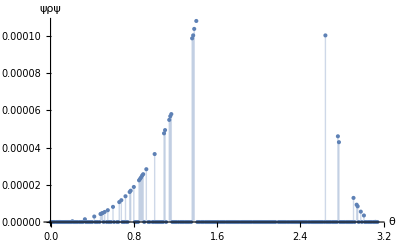

```mathematica
ListPlot[
	Transpose[{params,fids}], 
	AxesLabel-> {"θ","ψρψ"},
	Filling->Bottom
]
```

Finally, we free the state-vectors from our machine and disconnect from quest_link (killing the process)

```mathematica
DestroyAllQuregs[];
```

```mathematica
DestroyQuESTEnv[env];
```